Estimating Tension on the system

```mathematica
Subscript[y, min] = 0.5;
Subscript[L, c0]=20.5;
g = 9.8;
Subscript[m, s]= 16;
Subscript[L, cxs]=0.24;
testtension= {(g Subscript[L, cxs] Subscript[m, s] (Subscript[L, cs]-Subscript[x, s]))/(y Subscript[L, cs])/. {y -> √(Subscript[L, cxs]^2-((-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])^2)/(4 Subscript[L, cs]^2)), Subscript[x, s] -> (-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])/(2 Subscript[L, cs])}}/.{Subscript[L, cs]-> 20,Subscript[L, c]->Subscript[L, c0]-(-2 Subscript[d, pdp]+√(Subscript[d, ap]^2-2 Cos[Subscript[α, 1]] Subscript[d, ap] Subscript[L, arm]+Subscript[L, arm]^2)+√(Subscript[d, ap]^2-2 Cos[Subscript[α, 2]] Subscript[d, ap] Subscript[L, arm]+Subscript[L, arm]^2)+√((Subscript[d, ap]+Subscript[d, pdp])^2-2 Cos[Subscript[α, 1]] (Subscript[d, ap]+Subscript[d, pdp]) Subscript[L, arm]+Subscript[L, arm]^2)+√((Subscript[d, ap]+Subscript[d, pdp])^2-2 Cos[Subscript[α, 2]] (Subscript[d, ap]+Subscript[d, pdp]) Subscript[L, arm]+Subscript[L, arm]^2) /. {Subscript[d, ap] -> 0.2, Subscript[d, pdp] -> 0.1542, Subscript[L, arm] -> 0.25, Subscript[α, 1] -> 71.52575931 * Pi / 180})}
```

{(1.8816 (20+1/40 (-400-0.48 (20.1792-√(0.187958-0.1771 Cos[α_2])-√(0.1025-0.1 Cos[α_2]))+(20.1792-√(0.187958-0.1771 Cos[α_2])-√(0.1025-0.1 Cos[α_2]))^2)))/(√(0.0576-1/1600(400+0.48 (20.1792-√(0.187958-0.1771 Cos[α_2])-√(0.1025-0.1 Cos[α_2]))-(20.1792-√(0.187958-0.1771 Cos[α_2])-√(0.1025-0.1 Cos[α_2]))^2)^2))}

The context for this plot is that when first testing arm transitions, the arm that was lowering was around 5-10 degrees over its setpoint by the time the other arm hit its desired position. This is to see the resulting tension from this overtensioned state.

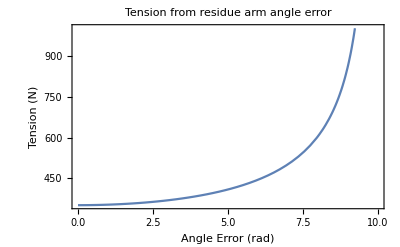

```mathematica
Plot[testtension /. {Subscript[α, 2]-> a * Pi/180}, {a, 0, 10}, PlotLabel-> "Tension from residue arm angle error",Frame-> True,  FrameLabel->{"Angle Error (rad)","Tension (N)"}]
```

Deriving equation for estimating torque for an arm

```mathematica
FullSimplify[T Subscript[L, arm] Sin[ArcTan[(Subscript[L, arm] Sin[α])/(Subscript[L, arm] Cos[α] - Subscript[d, ap])] - α] + T Subscript[L, arm] Sin[ArcTan[(Subscript[L, arm] Sin[α])/(Subscript[d, ap] + Subscript[d, pdp]-Subscript[L, arm] Cos[α])] - α] + m Subscript[L, arm]/2g Cos[α]] /. {Subscript[L,arm]->Larm,Subscript[d,ap]->dap,Subscript[d,pdp]->dpdp}
```

Larm (4.9 m Cos[α]-T (Sin[α+ArcTan[(Larm Sin[α])/(dap-Larm Cos[α])]]+Sin[α-ArcTan[(Larm Sin[α])/(dap+dpdp-Larm Cos[α])]]))

```mathematica
Torque[α_, Larm_, dap_, dpdp_]:=1/2 Larm (g m Cos[α]-2 T (Sin[α-ArcTan[(Larm Sin[α])/(dap-Larm Cos[α])]]+Sin[α+ArcTan[(Larm Sin[α])/(dap+dpdp-Larm Cos[α])]]))
```

If we assume around 400 N of tension at the stake rail and estimate the hytorc gearing to be about 5049 and cap the maximum motor torque at 200 mNm, we can calculate the percent power needed to move the arm at the ends. Notice that its quite small, thus ensuring that we can accurately control our arm position without having to account for the changing tension throughout the arm transition.

```mathematica
(Torque[109 * Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 400}) / 5049 / 0.2
```

-0.148771

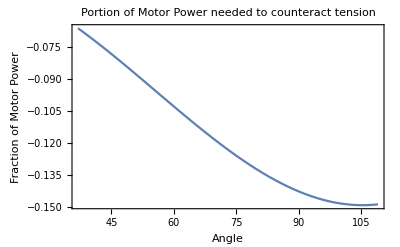

```mathematica
Plot[(Torque[α* Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 400})/ 5049 / 0.2, {α, 37, 109}, PlotLabel-> "Portion of Motor Power needed to counteract tension",Frame-> True,  FrameLabel->{"Angle","Fraction of Motor Power"}]
```

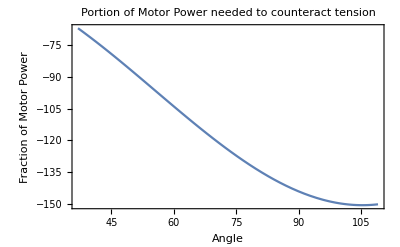

```mathematica
Plot[(Torque[α* Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 400}), {α, 37, 109}, PlotLabel-> "Portion of Motor Power needed to counteract tension",Frame-> True,  FrameLabel->{"Angle","Fraction of Motor Power"}]
```

```mathematica
endtension = {(g Subscript[L, cxs] Subscript[m, s] (Subscript[L, cs]-Subscript[x, s]))/(y Subscript[L, cs])/. {y -> √(Subscript[L, cxs]^2-((-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])^2)/(4 Subscript[L, cs]^2)), Subscript[x, s] -> (-Subscript[L, c]^2+Subscript[L, cs]^2+2 Subscript[L, c] Subscript[L, cxs])/(2 Subscript[L, cs])}}/.{Subscript[L, c]->Sqrt[Subscript[L, cs]^2 + 4 * Subscript[y, min]^2]}
```

{(37.632 (L_cs-(-1.+0.48 √(1.+L_cs^2))/(2 L_cs)))/(L_cs √(0.0576-((-1.+0.48 √(1.+L_cs^2))^2)/(4 L_cs^2)))}

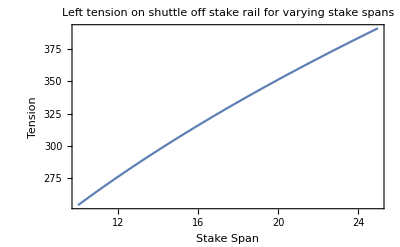

```mathematica
Plot[endtension, {Subscript[L, cs], 10, 25}, PlotLabel-> "Left tension on shuttle off stake rail for varying stake spans",Frame-> True,  FrameLabel->{"Stake Span","Tension"}]
```

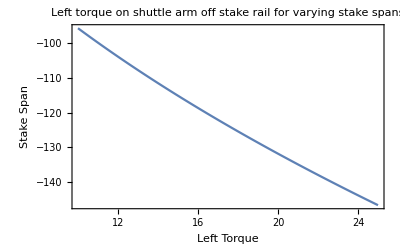

```mathematica
Plot[Torque[109 * Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> endtension}, {Subscript[L, cs], 10, 25}, PlotLabel-> "Left torque on shuttle arm off stake rail for varying stake spans",Frame-> True,  FrameLabel->{"Left Torque","Stake Span"}]
```

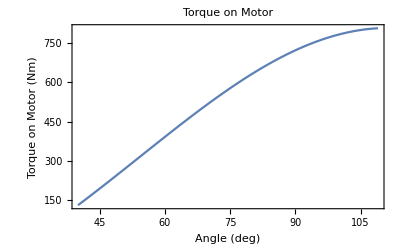

```mathematica
Plot[(-Torque[α* Pi / 180, 0.25, 0.2, 0.1542] /. {g -> 9.8, m -> .35, T -> 2000}), {α, 40, 109}, PlotLabel-> "Torque on Motor",Frame-> True,  FrameLabel->{"Angle (deg)","Torque on Motor (Nm)"}]
```

We can see that changing the stake spans will have a relatively negligible effect on the amount of torque needed to be exerted to control arm positions